```mathematica
Sum[Binomial[n/d,k](1-1/d)^k(1/d)^(n/d-k),{k,0,n/d/2}]
```

(1/d)^(n/(2 d)) ((1/d)^(n/(2 d)) d^(n/d)-((-1+d)/d)^(1+n/(2 d)) d Binomial[n/d,1+n/(2 d)] Hypergeometric2F1[1,1-n/(2 d),2+n/(2 d),1-d])

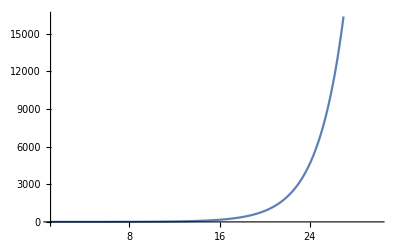

```mathematica
Plot[Binomial[n,n/d]%8/.d->5,{n,1,30}]
```

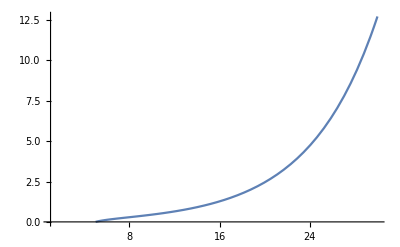

```mathematica
Plot[Binomial[n,n/d]((n/d-1)/n)^(n/d)/.d->5,{n,1,30}]
```

```mathematica
Graphics3D[{FaceForm[Opacity[0.05]],EdgeForm[Thick],Tetrahedron[]},Boxed->False]
```

-Graphics3D-

```mathematica
RegionPlot3D[{
x+y>=2z&&z+y>=x
},{x,0,1},{y,0,1},{z,0,1}]
```

-Graphics3D-

```mathematica
pol=Polyhedron[{{0,0,0},{1,1,0},{1,0,1},{0,1,1},{1,1,1}},{{1,2,3},{1,2,4},{1,4,3},{5,2,3},{5,2,4},{5,4,3}}]
Graphics3D[{Opacity[0.5],pol,FaceForm[Opacity[0.]],Cube[{1/2,1/2,1/2}]},Boxed->False]
```

Polyhedron[…]

-Graphics3D-